## myPackage

```mathematica
(*erstellt am 2025-05-03*)
(*CloudGet[
 CloudObject[
  "https://www.wolframcloud.com/obj/firlecarl/myPackageWL.wl"]]
  *)

myFontSize=13
myFontStandard="Lucida Sans Unicode"

myStyle["Wolfram Mathematica Version 14.2",22,Background->Yellow]
(*myColorFavorits = TableForm[Table[ColorData[i],{i,{3,24,35,61,97,106,114}}]]
Table[ContourPlot[x+Sin[x^2+y^2],{x,-4,4},{y,-4,4},Contours->9,ContourShading->ColorData[i,"ColorList"]],{i,{3,24,35,61,97,106,114}}]

myColorGradientFavorits=Table[DensityPlot[y+Sin[x^2+3y],{x,-3,3},{y,-3,3},ColorFunction->ColorData[i]],{i,{"RedBlueTones","Rainbow","DarkRainbow","DarkBands","BrightBands","CMYKColors","Pastel","GrayTones"}}]

Table[ColorData[i,"Image"],{i,{"DarkRainbow","Pastel"}}]*)

myColors=ColorData[61]
myColorForGradient=ColorData["DarkRainbow"]
myCMYKColors[]
myBAUAColors[4]

myExportFigureList={};
myExportEquationList={};

impPath = Directory[] ~~ "\\Desktop\\Mathematica\\Quelle\\" (*Import-Pfad anpassen*)
exPath = Directory[] ~~ "\\Desktop\\Mathematica\\Ausgabe\\" (*Export-Pfad anpassen*)

pathSaveVersions = 
 Directory[] ~~ "\\Desktop\\Versionsverlauf\\" (*Pfad für Versionsverlauf*)
NotebookOpen[
 CloudObject[
  "https://www.wolframcloud.com/obj/firlecarl/Versionsverlauf.nb"]]

myPackageInputPrint[]
```

13

Lucida Sans Unicode

myStyle[Wolfram Mathematica Version 14.2,22,Background→RGBColor[1, 1, 0]]

ColorDataFunction[…]

ColorDataFunction[…]

myCMYKColors[]

myBAUAColors[4]

C:\Users\mona_\Desktop\Mathematica\Quelle\

C:\Users\mona_\Desktop\Mathematica\Ausgabe\

C:\Users\mona_\Desktop\Versionsverlauf\

myPackageInputPrint[]

## myFigureIDs

```mathematica
IntegerString[#,10,3]&/@Range[50]  (*make the next output cell to an input cell with the variable myFigureIDs myFigureIDs=*)
```

```mathematica
myFigureIDs={"001","002","003","004","005","006","007","008","009","010","011","012","013","014","015","016","017","018","019","020","021","022","023","024","025","026","027","028","029","030","031","032","033","034","035","036","037","038","039","040","041","042","043","044","045","046","047","048","049","050"}
```

{001,002,003,004,005,006,007,008,009,010,011,012,013,014,015,016,017,018,019,020,021,022,023,024,025,026,027,028,029,030,031,032,033,034,035,036,037,038,039,040,041,042,043,044,045,046,047,048,049,050}

## regression RIP signal and lung volume

```mathematica
CloudGet[
 CloudObject[
  "https://www.wolframcloud.com/obj/firlecarl/myPackageWL.wl"]];

NotebookEvaluate["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2024_effects-mask-wearing/raw-data-import-functions.nb"];

urlHead="https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2024_effects-mask-wearing/20251127-01_rip_spiro/20260108-01/";
```

```mathematica
dProtocolImport["20260108-01_protocol.txt"]
```

Import successful

```mathematica
protocol
```

{start time***Thu Jan 08 2026 11:03:39 GMT+0100 (Mitteleuropäische Normalzeit)→0. s,comment***test vernier RIP via Bluetooth with PExA flow meter measurement, 1908 = RIP thorax, 14v9 = abdomen→102.497 s,RIP_1_start→188.551 s,RIP_2_start→189.122 s,pexa_start→473.122 s,pexa_end→677.549 s,RIP_2_end→684.75 s,RIP_1_end→685.171 s,end of protocol→686.171 s}

```mathematica
dPexaImport["20260108-01_pexa.txt","pexa"]
```

```mathematica
createTabular[]
```

C:\Users\mona_\Desktop\Mathematica\Ausgabe\data_20260108-01.m

```mathematica
Flatten[varNames][[-2]]
```

pexa_Inhale Exhale Airflow [ml/s]

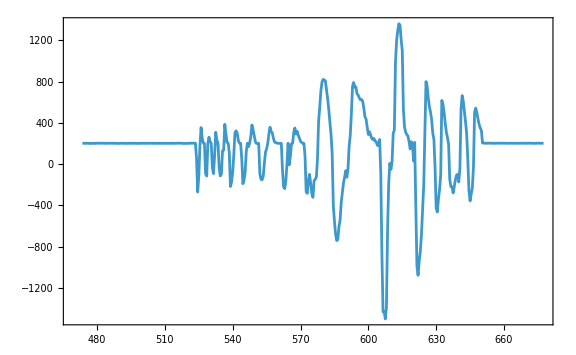

```mathematica
ListLinePlot[#,myPlotSequence[],PlotRange->All]&@Transpose[{oneTable[[1]],(oneTable[[-2]] /. "n.a."->Null)}]
```

### lung volume

```mathematica
protocol
```

{start time***Thu Jan 08 2026 11:03:39 GMT+0100 (Mitteleuropäische Normalzeit)→0. s,comment***test vernier RIP via Bluetooth with PExA flow meter measurement, 1908 = RIP thorax, 14v9 = abdomen→102.497 s,RIP_1_start→188.551 s,RIP_2_start→189.122 s,pexa_start→473.122 s,pexa_end→677.549 s,RIP_2_end→684.75 s,RIP_1_end→685.171 s,end of protocol→686.171 s}

```mathematica
dRIPImport["20260108-01_rip.csv","RIP_1"]
dRIPImport["20260108-01_rip.csv","RIP_2",-2]
```

```mathematica
varNames
```

{elapsed time [s],{pexa_DeltaTime OPC [s],pexa_Particle 1 [1/L],pexa_Particle 2 [1/L],pexa_Particle 3 [1/L],pexa_Particle 4 [1/L],pexa_Particle 5 [1/L],pexa_Particle 6 [1/L],pexa_Particle 7 [1/L],pexa_Particle 8 [1/L],pexa_Particle 9 [1/L],pexa_Particle 10 [1/L],pexa_Particle 11 [1/L],pexa_Particle 12 [1/L],pexa_Particle 13 [1/L],pexa_Particle 14 [1/L],pexa_Particle 15 [1/L],pexa_Particle 16 [1/L],pexa_Particle Sum [1/L],pexa_Accumulated mass [ng],pexa_Accumulated volume [l],pexa_Exhale Counter [1],pexa_Event Counter [1],pexa_Internal Temperature [Celsius],pexa_Internal Humidity [percent],pexa_Temperature too low [1],pexa_Temperature too high [1],pexa_Circuit Flow [ml/s],pexa_Temperature Impactor [Celsius],pexa_Temperature Reservoir [Celsius],pexa_Inhale Airflow [ml/s],pexa_Inhale Exhale Airflow [ml/s],pexa_Volume [ml]},RIP_1 force ribcage [N],RIP_2 force ribcage [N]}

```mathematica
Length@Flatten[varNames]
```

35

```mathematica
Length[oneTable]
```

36

```mathematica
test=StringSplit["Date/Time\tExhale Airflow [ml/s]\tDeltaTime OPC [s]\tParticle 1 [counts/l]\tParticle 2 [counts/l]\tParticle 3 [counts/l]\tParticle 4 [counts/l]\tParticle 5 [counts/l]\tParticle 6 [counts/l]\tParticle 7 [counts/l]\tParticle 8 [counts/l]\tParticle 9 [counts/l]\tParticle 10 [counts/l]\tParticle 11 [counts/l]\tParticle 12 [counts/l]\tParticle 13 [counts/l]\tParticle 14 [counts/l]\tParticle 15 [counts/l]\tParticle 16 [counts/l]\tParticle Sum [counts/l]\tAccumulated mass [ng]\tAccumulated volume [l]\tExhale Counter [n]\tEvent Counter [n]\tInternal Temperature [°C]\tInternal Humidity [%]\tTemperature too low [n]\tTemperature too high [n]\tCircuit Flow [ml/s]\tTemperature Impactor [°C]\tTemperature Reservoir [°C]\tInhale Airflow [ml/s]\tInhale Exhale Airflow [ml/s]\tVolume ml]","\t"]
```

{Date/Time,Exhale Airflow [ml/s],DeltaTime OPC [s],Particle 1 [counts/l],Particle 2 [counts/l],Particle 3 [counts/l],Particle 4 [counts/l],Particle 5 [counts/l],Particle 6 [counts/l],Particle 7 [counts/l],Particle 8 [counts/l],Particle 9 [counts/l],Particle 10 [counts/l],Particle 11 [counts/l],Particle 12 [counts/l],Particle 13 [counts/l],Particle 14 [counts/l],Particle 15 [counts/l],Particle 16 [counts/l],Particle Sum [counts/l],Accumulated mass [ng],Accumulated volume [l],Exhale Counter [n],Event Counter [n],Internal Temperature [°C],Internal Humidity [%],Temperature too low [n],Temperature too high [n],Circuit Flow [ml/s],Temperature Impactor [°C],Temperature Reservoir [°C],Inhale Airflow [ml/s],Inhale Exhale Airflow [ml/s],Volume ml]}

```mathematica
test[[4;;20]]
```

{Particle 1 [counts/l],Particle 2 [counts/l],Particle 3 [counts/l],Particle 4 [counts/l],Particle 5 [counts/l],Particle 6 [counts/l],Particle 7 [counts/l],Particle 8 [counts/l],Particle 9 [counts/l],Particle 10 [counts/l],Particle 11 [counts/l],Particle 12 [counts/l],Particle 13 [counts/l],Particle 14 [counts/l],Particle 15 [counts/l],Particle 16 [counts/l],Particle Sum [counts/l]}

```mathematica
Length[%30]
```

34

```mathematica
TableForm[Transpose[{Flatten@varNames,oneTable[[All,-50;;-1]]}]]
```

Transpose::nmtx: The first two levels of {{elapsed time [s],pexa_DeltaTime OPC [s],pexa_Particle 1 [1/L],pexa_Particle 2 [1/L],pexa_Particle 3 [1/L],pexa_Particle 4 [1/L],pexa_Particle 5 [1/L],pexa_Particle 6 [1/L],pexa_Particle 7 [1/L],pexa_Particle 8 [1/L],«16»,pexa_Temperature too high [1],pexa_Circuit Flow [ml/s],pexa_Temperature Impactor [Celsius],pexa_Temperature Reservoir [Celsius],pexa_Inhale Airflow [ml/s],pexa_Inhale Exhale Airflow [ml/s],pexa_Volume [ml],RIP_1 force ribcage [N],RIP_2 force ribcage [N]},{{«1»},«35»}} cannot be transposed.

Transpose[{{elapsed time [s],pexa_DeltaTime OPC [s],pexa_Particle 1 [1/L],pexa_Particle 2 [1/L],pexa_Particle 3 [1/L],pexa_Particle 4 [1/L],pexa_Particle 5 [1/L],pexa_Particle 6 [1/L],pexa_Particle 7 [1/L],pexa_Particle 8 [1/L],pexa_Particle 9 [1/L],pexa_Particle 10 [1/L],pexa_Particle 11 [1/L],pexa_Particle 12 [1/L],pexa_Particle 13 [1/L],pexa_Particle 14 [1/L],pexa_Particle 15 [1/L],pexa_Particle 16 [1/L],pexa_Particle Sum [1/L],pexa_Accumulated mass [ng],pexa_Accumulated volume [l],pexa_Exhale Counter [1],pexa_Event Counter [1],pexa_Internal Temperature [Celsius],pexa_Internal Humidity [percent],pexa_Temperature too low [1],pexa_Temperature too high [1],pexa_Circuit Flow [ml/s],pexa_Temperature Impactor [Celsius],pexa_Temperature Reservoir [Celsius],pexa_Inhale Airflow [ml/s],pexa_Inhale Exhale Airflow [ml/s],pexa_Volume [ml],RIP_1 force ribcage [N],RIP_2 force ribcage [N]},{{662.,662.5,663.,663.5,664.,664.5,665.,665.5,666.,666.5,667.,667.5,668.,668.5,669.,669.5,670.,670.5,671.,671.5,672.,672.5,673.,673.5,674.,674.5,675.,675.5,676.,676.5,677.,677.5,678.,678.5,679.,679.5,680.,680.5,681.,681.5,682.,682.5,683.,683.5,684.,684.5,685.,685.5,686.,686.5},{202.16,202.297,202.285,202.709,202.529,202.052,202.68,201.782,201.544,202.692,201.931,202.884,203.17,202.543,202.969,201.66,202.557,202.164,202.756,203.65,202.34,202.469,201.268,202.038,202.207,202.584,203.562,202.608,202.741,202.218,202.45,202.769,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{1.000.10,n.a.,1.000.10,n.a.,1.000.10,n.a.,1.000.10,n.a.,1.000.10,n.a.,1.000.10,n.a.,1.000.10,0.950.09,n.a.,n.a.,1.020.10,n.a.,1.000.10,n.a.,1.010.10,n.a.,1.000.10,n.a.,1.000.10,n.a.,1.080.11,0.900.09,n.a.,n.a.,1.000.10,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{600.60.,n.a.,600.60.,n.a.,450.45.,n.a.,600.60.,n.a.,350.35.,n.a.,250.25.,n.a.,700.70.,650.65.,n.a.,n.a.,750.75.,n.a.,600.60.,n.a.,550.55.,n.a.,1000.100.,n.a.,400.40.,n.a.,150.15.,850.85.,n.a.,n.a.,500.50.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{350.35.,n.a.,100.10.,n.a.,350.35.,n.a.,100.10.,n.a.,350.35.,n.a.,250.25.,n.a.,350.35.,400.40.,n.a.,n.a.,250.25.,n.a.,450.45.,n.a.,200.20.,n.a.,150.15.,n.a.,250.25.,n.a.,350.35.,350.35.,n.a.,n.a.,150.15.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{50.5.,n.a.,150.15.,n.a.,100.10.,n.a.,50.5.,n.a.,50.5.,n.a.,0,n.a.,250.25.,300.30.,n.a.,n.a.,250.25.,n.a.,50.5.,n.a.,200.20.,n.a.,100.10.,n.a.,0,n.a.,50.5.,100.10.,n.a.,n.a.,100.10.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{50.5.,n.a.,0,n.a.,50.5.,n.a.,150.15.,n.a.,0,n.a.,0,n.a.,50.5.,0,n.a.,n.a.,50.5.,n.a.,0,n.a.,50.5.,n.a.,0,n.a.,50.5.,n.a.,100.10.,0,n.a.,n.a.,0,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{0,n.a.,50.5.,n.a.,0,n.a.,0,n.a.,50.5.,n.a.,0,n.a.,50.5.,0,n.a.,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,50.5.,50.5.,n.a.,n.a.,0,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,50.5.,n.a.,50.5.,0,n.a.,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,50.5.,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{1050.,n.a.,900.,n.a.,950.,n.a.,900.,n.a.,800.,n.a.,550.,n.a.,1450.,1350.,n.a.,n.a.,1350.,n.a.,1100.,n.a.,1000.,n.a.,1250.,n.a.,700.,n.a.,700.,1350.,n.a.,n.a.,750.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{0.166959,n.a.,0.172093,n.a.,0.175293,n.a.,0.180963,n.a.,0.185673,n.a.,0.19231,n.a.,0.206083,0.209121,n.a.,n.a.,0.259387,n.a.,0.261077,n.a.,0.26478,n.a.,0.266654,n.a.,0.26901,n.a.,0.277147,0.282089,n.a.,n.a.,0.283472,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{53.3275,n.a.,53.5297,n.a.,53.7322,n.a.,53.9345,n.a.,54.1367,n.a.,54.3388,n.a.,54.5413,54.7239,n.a.,n.a.,54.9464,n.a.,55.1488,n.a.,55.352,n.a.,55.5544,n.a.,55.756,n.a.,55.9584,56.1413,n.a.,n.a.,56.364,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,n.a.,0,0,n.a.,n.a.,0,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{27.5,n.a.,27.5,n.a.,27.5,n.a.,27.5,n.a.,27.5,n.a.,27.5,n.a.,27.4,27.4,n.a.,n.a.,27.4,n.a.,27.4,n.a.,27.4,n.a.,27.4,n.a.,27.5,n.a.,27.5,27.5,n.a.,n.a.,27.5,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{35.4,n.a.,35.4,n.a.,35.4,n.a.,35.4,n.a.,35.4,n.a.,35.4,n.a.,35.4,35.4,n.a.,n.a.,35.4,n.a.,35.4,n.a.,35.4,n.a.,35.4,n.a.,35.4,n.a.,35.4,35.4,n.a.,n.a.,35.4,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{1.,n.a.,1.,n.a.,1.,n.a.,1.,n.a.,1.,n.a.,1.,n.a.,1.,1.,n.a.,n.a.,1.,n.a.,1.,n.a.,1.,n.a.,1.,n.a.,1.,n.a.,1.,1.,n.a.,n.a.,1.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{0.,n.a.,0.,n.a.,0.,n.a.,0.,n.a.,0.,n.a.,0.,n.a.,0.,0.,n.a.,n.a.,0.,n.a.,0.,n.a.,0.,n.a.,0.,n.a.,0.,n.a.,0.,0.,n.a.,n.a.,0.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{251.464,249.977,249.571,248.017,247.899,249.134,249.742,251.532,251.601,249.845,250.217,248.34,248.304,249.48,250.836,252.48,250.98,250.346,249.168,248.729,249.904,250.923,252.605,251.275,249.917,249.539,247.875,249.33,250.193,252.056,251.507,250.622,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{36.48,n.a.,36.46,n.a.,36.47,n.a.,36.47,n.a.,36.47,n.a.,36.47,n.a.,36.47,36.48,n.a.,n.a.,36.47,n.a.,36.47,n.a.,36.46,n.a.,36.44,n.a.,36.47,n.a.,36.46,36.46,n.a.,n.a.,36.47,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{36.08,n.a.,36.08,n.a.,36.09,n.a.,36.07,n.a.,36.09,n.a.,36.08,n.a.,36.08,36.07,n.a.,n.a.,36.09,n.a.,36.07,n.a.,36.09,n.a.,36.07,n.a.,36.08,n.a.,36.07,36.08,n.a.,n.a.,36.09,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{0.0133809,0.013832,0.0173163,-0.0036224,0.0112445,7.94×10^-6,0.00626946,0.00159616,0.00635606,0.00317106,0.0055918,0.0099558,0.012471,0.00453874,0.0148104,0.0004369,0.0106747,0.0168083,0.00686516,0.00467942,0.0143523,0.0144435,0.0218866,0.00565008,0.00046146,0.00621952,0.0175491,0.00693486,0.0121625,0.0200172,0.00872062,0.0168084,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{202.16,202.297,202.285,202.709,202.529,202.052,202.68,201.782,201.544,202.692,201.931,202.884,203.17,202.543,202.969,201.66,202.557,202.164,202.756,203.65,202.34,202.469,201.268,202.038,202.207,202.584,203.562,202.608,202.741,202.218,202.45,202.769,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{-23085.2,-23186.4,-23287.5,-23388.8,-23490.1,-23591.2,-23692.4,-23793.6,-23894.3,-23995.4,-24096.5,-24197.7,-24299.3,-24400.7,-24502.1,-24603.2,-24704.3,-24805.5,-24906.6,-25008.4,-25109.8,-25211.1,-25312.,-25412.8,-25513.8,-25615.,-25716.6,-25818.2,-25919.4,-26020.8,-26121.8,-26202.9,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.},{7.09154,7.08132,6.92547,7.01872,6.35698,6.37614,6.00566,6.17174,7.94874,9.32845,9.27862,10.5152,8.31283,7.91425,8.13143,8.05478,7.93597,7.80566,7.69197,7.53356,7.63448,9.59033,11.2587,10.7656,9.6376,9.20708,9.07933,8.81233,8.4738,9.29012,10.6941,9.27607,8.50957,8.58494,10.8142,10.4156,9.87011,10.795,9.48047,8.77018,8.599,8.26301,8.15314,9.28629,10.8206,10.6008,9.18153,n.a.,n.a.,n.a.},{9.55925,9.31482,9.06869,8.42824,9.4102,9.08231,6.45066,8.35159,11.3341,13.482,13.3517,12.9174,8.86003,7.57231,7.49055,7.39346,7.23931,7.05109,6.97274,6.6985,7.39942,10.5259,10.749,7.42923,6.48729,6.64996,6.99914,6.63207,8.01347,12.0793,10.0702,7.11752,6.98125,8.87536,9.99871,7.78948,9.8173,8.74506,7.3347,6.72661,5.52065,4.64172,5.61092,9.12319,10.7592,7.34747,6.62185,n.a.,n.a.,n.a.}}}]

```mathematica
createTabular[]
```

C:\Users\mona_\Desktop\Mathematica\Ausgabe\data_20260108-01.m

```mathematica
Clear[s,L,l,ml,ng,ug,cm3,m3,Watt,ppm,mbar,Celsius,percent,n];
varNamesList=StringReplace[#,"[N]"->"[n]"]&/@Flatten[varNames]
quantities=ToExpression[Flatten[StringCases[#,"["~~a__~~"]"->a]&/@varNamesList]] /. {s->"Seconds",L->"Liters",l->"Liters",ml->"Milliliters",ng->"nanogram",ug->"Micrograms",cm3->("Centimeters"^3),m3->("Meters"^3),Watt->"Watts",ppm->"PartsPerMillion",mbar->"Millibars",Celsius->"DegreesCelsius",percent->"Percent",n->"Newtons"}
temp=oneTable/. "n.a."->Missing[]
temp=Table[temp[[i]]=(Quantity[#,quantities[[i]]]&/@temp[[i]]),{i,Length[quantities]}];
ToTabular[Transpose[temp],"Rows",<|"ColumnKeys"->Flatten[varNames]|>]
```

```mathematica
temp[[-1]][[All,1]]===oneTable[[-1]]
```

```mathematica
oneTableTab[[All,"RIP_1 force ribcage [N]"]] //Normal
```

```mathematica
N
```

N

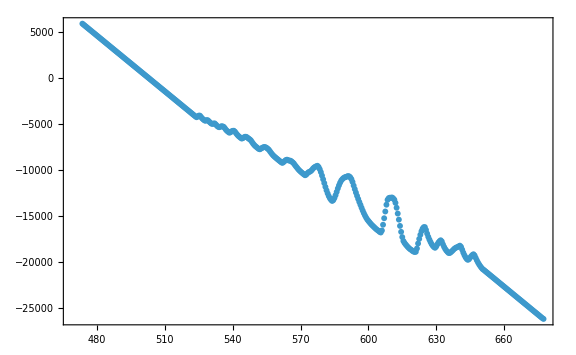

```mathematica
ListPlot[oneTableTab->{"elapsed time [s]","RIP_1 force ribcage [N]"},myPlotSequence[],PlotRange->All]
```

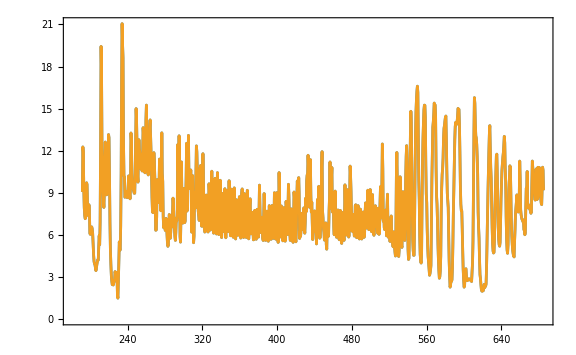

```mathematica
ListLinePlot[#,myPlotSequence[],PlotRange->All]&@({Transpose[{oneTable[[1]],(oneTable[[-2]] /. "n.a."->Null)}],Transpose[{oneTable[[1]],oneTable[[-2]] }]}/. "n.a."->Null)
```

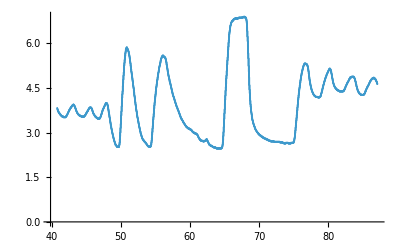
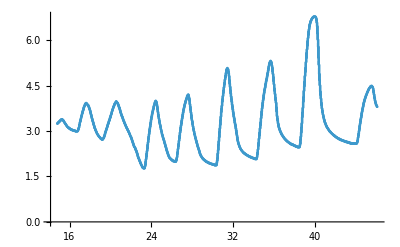
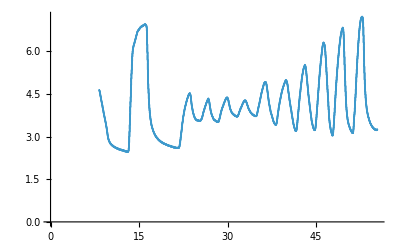
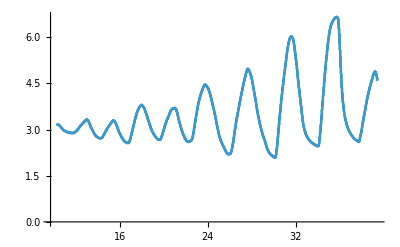
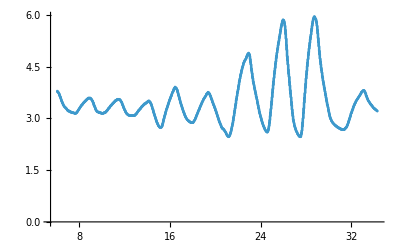
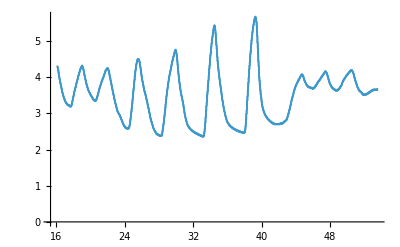
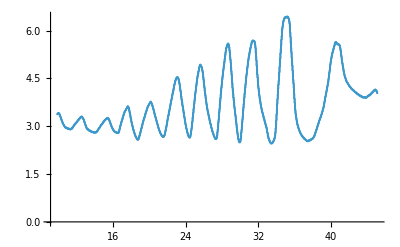
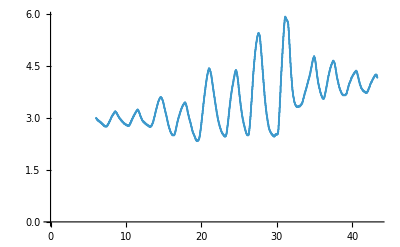

```mathematica
spiroTimeDeltaCorrection=.
spiroTimeDeltaCorrection[list_List]:=Module[{diff,lasttime,temp,tempAll},
Map[(lasttime=#[[2,-1,1]];
diff=#[[1]]-lasttime;
temp=#[[2,All,1]]+diff;
tempAll=#;
tempAll[[2,All,1]]=temp;
#[[-1]]->tempAll[[2]]
)&
,list
]
]

spiroDataTimeCalibrated=spiroTimeDeltaCorrection[Transpose[{times[[parts]][[All,-2]],points,filenames[[parts]]}]];
ListPlot[#[[2]]]&/@spiroDataTimeCalibrated
```

```mathematica
Abs[Subtract@@MinMax@#[[2,All,2]]] &/@spiroDataTimeCalibrated
```

{4.44068,5.01695,4.76271,4.59322,3.49153,3.32203,3.98305,3.59322}

```mathematica
spiroDataTimeCalibrated
```

```mathematica
smoothSpiroData=.
smoothSpiroData[l_]:=l[[1]]->((Normal[Mean[#[[All,2]]]&/@GroupBy[l[[2]],First]]) /. (Rule->List))

spiroDataTimeCalibratedSmoothed=smoothSpiroData[#]&/@spiroDataTimeCalibrated
```

### RIP data

```mathematica
allRIPData=(path="https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2024_effects-mask-wearing/20250327-01_rip_spiro/data-files/"~~#~~".csv";If[URLRead[path]["StatusCode"]==200,#->Import[path],Nothing])&/@filenames
```

```mathematica
TableForm[allRIPData[[-1,2,1;;5]]] (*die Datensätze wurden beim Export vom Vernier Programm zusammengehängt. Der letzte Datensatz enthält alle Messreihen!*)
```

Datensatz 1:Zeit(s) | Datensatz 1:Force 1(N) | Datensatz 1:Respiration Rate 1(bpm) | Datensatz 1:Force 2(N) | Datensatz 1:Respiration Rate 2(bpm) | Datensatz 2:Zeit(s) | Datensatz 2:Force 1(N) | Datensatz 2:Respiration Rate 1(bpm) | Datensatz 2:Force 2(N) | Datensatz 2:Respiration Rate 2(bpm) | Datensatz 3:Zeit(s) | Datensatz 3:Force 1(N) | Datensatz 3:Respiration Rate 1(bpm) | Datensatz 3:Force 2(N) | Datensatz 3:Respiration Rate 2(bpm) | Datensatz 4:Zeit(s) | Datensatz 4:Force 1(N) | Datensatz 4:Respiration Rate 1(bpm) | Datensatz 4:Force 2(N) | Datensatz 4:Respiration Rate 2(bpm) | Datensatz 5:Zeit(s) | Datensatz 5:Force 1(N) | Datensatz 5:Respiration Rate 1(bpm) | Datensatz 5:Force 2(N) | Datensatz 5:Respiration Rate 2(bpm) | Datensatz 6:Zeit(s) | Datensatz 6:Force 1(N) | Datensatz 6:Respiration Rate 1(bpm) | Datensatz 6:Force 2(N) | Datensatz 6:Respiration Rate 2(bpm) | Datensatz 7:Zeit(s) | Datensatz 7:Force 1(N) | Datensatz 7:Respiration Rate 1(bpm) | Datensatz 7:Force 2(N) | Datensatz 7:Respiration Rate 2(bpm) | Datensatz 8:Zeit(s) | Datensatz 8:Force 1(N) | Datensatz 8:Respiration Rate 1(bpm) | Datensatz 8:Force 2(N) | Datensatz 8:Respiration Rate 2(bpm) | Datensatz 9:Zeit(s) | Datensatz 9:Force 1(N) | Datensatz 9:Respiration Rate 1(bpm) | Datensatz 9:Force 2(N) | Datensatz 9:Respiration Rate 2(bpm) | Datensatz 10:Zeit(s) | Datensatz 10:Force 1(N) | Datensatz 10:Respiration Rate 1(bpm) | Datensatz 10:Force 2(N) | Datensatz 10:Respiration Rate 2(bpm) | Datensatz 11:Zeit(s) | Datensatz 11:Force 1(N) | Datensatz 11:Respiration Rate 1(bpm) | Datensatz 11:Force 2(N) | Datensatz 11:Respiration Rate 2(bpm) | Datensatz 12:Zeit(s) | Datensatz 12:Force 1(N) | Datensatz 12:Respiration Rate 1(bpm) | Datensatz 12:Force 2(N) | Datensatz 12:Respiration Rate 2(bpm) | Datensatz 13:Zeit(s) | Datensatz 13:Force 1(N) | Datensatz 13:Respiration Rate 1(bpm) | Datensatz 13:Force 2(N) | Datensatz 13:Respiration Rate 2(bpm) | Datensatz 14:Zeit(s) | Datensatz 14:Force 1(N) | Datensatz 14:Respiration Rate 1(bpm) | Datensatz 14:Force 2(N) | Datensatz 14:Respiration Rate 2(bpm) | Datensatz 15:Zeit(s) | Datensatz 15:Force 1(N) | Datensatz 15:Respiration Rate 1(bpm) | Datensatz 15:Force 2(N) | Datensatz 15:Respiration Rate 2(bpm) | Datensatz 16:Zeit(s) | Datensatz 16:Force 1(N) | Datensatz 16:Respiration Rate 1(bpm) | Datensatz 16:Force 2(N) | Datensatz 16:Respiration Rate 2(bpm) | Datensatz 17:Zeit(s) | Datensatz 17:Force 1(N) | Datensatz 17:Respiration Rate 1(bpm) | Datensatz 17:Force 2(N) | Datensatz 17:Respiration Rate 2(bpm) | Datensatz 18:Zeit(s) | Datensatz 18:Force 1(N) | Datensatz 18:Respiration Rate 1(bpm) | Datensatz 18:Force 2(N) | Datensatz 18:Respiration Rate 2(bpm) | Datensatz 19:Zeit(s) | Datensatz 19:Force 1(N) | Datensatz 19:Respiration Rate 1(bpm) | Datensatz 19:Force 2(N) | Datensatz 19:Respiration Rate 2(bpm)
0. | 14.8856 | 22.3729 | 12.2965 | 22.3577 | 0. | 10.5293 | 21.398 | 8.47167 | 21.4133 | 0. | 12.8084 | 20.7612 | 10.1018 | 20.7756 | 0. | 14.3618 | 0. | 10.9091 | 14.4578 | 0. | 16.2346 | 22.0147 | 11.2106 | 18.012 | 0. | 12.5554 | 21.9619 | 8.96478 | 21.9619 | 0. | 10.3147 | 9.91736 | 8.25705 | 9.90099 | 0. | 10.7439 | 16.632 | 9.34293 | 14.5935 | 0. | 10.0387 | 20.3313 | 7.38835 | 20.4255 | 0. | 11.2626 | 21.2598 | 7.75627 | 20.2551 | 0. | 12.6704 | 12.5174 | 8.97756 | 12.4138 | 0. | 10.5651 | 0. | 7.99644 | 0. | 0. | 12.3331 | 0 | 9.44768 | 19.4384 | 0. | 8.64626 | 0. | 7.12774 | 19.4085 | 0. | 9.85989 | 6.23701 | 7.5672 | 0 | 0. | 7.91808 | 6.85453 | 6.67551 | 14.7472 | 0. | 12.2999 | 8.79765 | 8.49467 | 17.2579 | 0. | 10.7541 | 21.7077 | 7.83037 | 20.0267 | 0. | 7.17203 | 0. | 6.34846 | 8.44278
0.1 | 13.9734 | Missing[NotAvailable] | 11.7421 | Missing[NotAvailable] | 0.1 | 11.5896 | Missing[NotAvailable] | 9.11553 | Missing[NotAvailable] | 0.1 | 11.4798 | Missing[NotAvailable] | 9.38636 | Missing[NotAvailable] | 0.1 | 12.6985 | Missing[NotAvailable] | 9.93568 | Missing[NotAvailable] | 0.1 | 16.7405 | Missing[NotAvailable] | 11.4252 | Missing[NotAvailable] | 0.1 | 14.1318 | Missing[NotAvailable] | 9.93313 | Missing[NotAvailable] | 0.1 | 9.73213 | Missing[NotAvailable] | 8.06032 | Missing[NotAvailable] | 0.1 | 9.45109 | Missing[NotAvailable] | 8.49722 | Missing[NotAvailable] | 0.1 | 11.679 | Missing[NotAvailable] | 8.25705 | Missing[NotAvailable] | 0.1 | 10.7107 | Missing[NotAvailable] | 7.79971 | Missing[NotAvailable] | 0.1 | 11.237 | Missing[NotAvailable] | 8.55598 | Missing[NotAvailable] | 0.1 | 11.0837 | Missing[NotAvailable] | 8.11141 | Missing[NotAvailable] | 0.1 | 11.5462 | Missing[NotAvailable] | 8.95712 | Missing[NotAvailable] | 0.1 | 8.19658 | Missing[NotAvailable] | 6.81603 | Missing[NotAvailable] | 0.1 | 9.47408 | Missing[NotAvailable] | 7.2376 | Missing[NotAvailable] | 0.1 | 7.59104 | Missing[NotAvailable] | 6.69083 | Missing[NotAvailable] | 0.1 | 13.0639 | Missing[NotAvailable] | 8.88814 | Missing[NotAvailable] | 0.1 | 9.90332 | Missing[NotAvailable] | 7.37813 | Missing[NotAvailable] | 0.1 | 7.20013 | Missing[NotAvailable] | 6.43533 | Missing[NotAvailable]
0.2 | 12.7036 | Missing[NotAvailable] | 10.9117 | Missing[NotAvailable] | 0.2 | 13.0996 | Missing[NotAvailable] | 9.97146 | Missing[NotAvailable] | 0.2 | 10.1052 | Missing[NotAvailable] | 8.67352 | Missing[NotAvailable] | 0.2 | 10.772 | Missing[NotAvailable] | 8.70928 | Missing[NotAvailable] | 0.2 | 16.7865 | Missing[NotAvailable] | 11.415 | Missing[NotAvailable] | 0.2 | 16.135 | Missing[NotAvailable] | 11.0011 | Missing[NotAvailable] | 0.2 | 9.13426 | Missing[NotAvailable] | 7.81248 | Missing[NotAvailable] | 0.2 | 8.06883 | Missing[NotAvailable] | 7.50077 | Missing[NotAvailable] | 0.2 | 13.7614 | Missing[NotAvailable] | 9.34037 | Missing[NotAvailable] | 0.2 | 10.0106 | Missing[NotAvailable] | 7.70773 | Missing[NotAvailable] | 0.2 | 9.54307 | Missing[NotAvailable] | 7.96067 | Missing[NotAvailable] | 0.2 | 11.0658 | Missing[NotAvailable] | 8.12164 | Missing[NotAvailable] | 0.2 | 10.4859 | Missing[NotAvailable] | 8.2826 | Missing[NotAvailable] | 0.2 | 7.71624 | Missing[NotAvailable] | 6.45833 | Missing[NotAvailable] | 0.2 | 9.36421 | Missing[NotAvailable] | 6.87735 | Missing[NotAvailable] | 0.2 | 7.58849 | Missing[NotAvailable] | 6.76237 | Missing[NotAvailable] | 0.2 | 13.5519 | Missing[NotAvailable] | 9.13086 | Missing[NotAvailable] | 0.2 | 8.79189 | Missing[NotAvailable] | 6.8518 | Missing[NotAvailable] | 0.2 | 7.43008 | Missing[NotAvailable] | 6.78537 | Missing[NotAvailable]
0.3 | 12.0623 | Missing[NotAvailable] | 10.4084 | Missing[NotAvailable] | 0.3 | 14.0271 | Missing[NotAvailable] | 10.393 | Missing[NotAvailable] | 0.3 | 9.91354 | Missing[NotAvailable] | 8.57642 | Missing[NotAvailable] | 0.3 | 10.4015 | Missing[NotAvailable] | 8.35414 | Missing[NotAvailable] | 0.3 | 16.02 | Missing[NotAvailable] | 11.0292 | Missing[NotAvailable] | 0.3 | 17.0292 | Missing[NotAvailable] | 11.2566 | Missing[NotAvailable] | 0.3 | 9.07294 | Missing[NotAvailable] | 7.70006 | Missing[NotAvailable] | 0.3 | 7.9513 | Missing[NotAvailable] | 7.26315 | Missing[NotAvailable] | 0.3 | 14.7604 | Missing[NotAvailable] | 9.64442 | Missing[NotAvailable] | 0.3 | 9.96208 | Missing[NotAvailable] | 7.54676 | Missing[NotAvailable] | 0.3 | 9.11893 | Missing[NotAvailable] | 7.53654 | Missing[NotAvailable] | 0.3 | 9.96208 | Missing[NotAvailable] | 7.88402 | Missing[NotAvailable] | 0.3 | 9.93143 | Missing[NotAvailable] | 8.03477 | Missing[NotAvailable] | 0.3 | 7.71368 | Missing[NotAvailable] | 6.48132 | Missing[NotAvailable] | 0.3 | 9.8139 | Missing[NotAvailable] | 6.93101 | Missing[NotAvailable] | 0.3 | 8.49807 | Missing[NotAvailable] | 7.03065 | Missing[NotAvailable] | 0.3 | 12.8876 | Missing[NotAvailable] | 8.87791 | Missing[NotAvailable] | 0.3 | 8.25279 | Missing[NotAvailable] | 6.72916 | Missing[NotAvailable] | 0.3 | 7.95386 | Missing[NotAvailable] | 7.32958 | Missing[NotAvailable]

```mathematica
ripData=Transpose[{allRIPData[[All,1]],allRIPData[[All,2,All,-5;;-1]][[All,All,{1,2,4}]]}]
```

```mathematica
ripData=#[[1]]->#[[2]]&/@(Transpose[{allRIPData[[All,1]],allRIPData[[All,2,All,-5;;-1]][[All,2;;-1,{1,2,4}]]}]/.({Missing["NotAvailable"],Missing["NotAvailable"],Missing["NotAvailable"]}->Nothing))
```

```mathematica
Transpose[{ filenames,times}]
```

{{13-52,{0.,11.587,86.626,163.838}},{13-58,{0.,10.215,87.148,96.617}},{14-07,{0.,7.21,46.161,95.607}},{14-09,{0.,6.607,55.385,76.168}},{14-12,{0.,6.155,39.394,51.1}},{14-16,{0.,4.767,34.314,45.389}},{14-18,{0.,16.13,53.533,60.223}},{14-21,{0.,5.265,45.151,69.111}},{14-25,{0.,4.027,43.35,48.236}},{14-28,{0.,4.538,32.585,48.87}},{14-30,{0.,4.698,34.442,48.932}},{14-34,{0.,18.158,64.024,77.825}}}

```mathematica
{#[[1]],#[[2,-1,1]]}&/@(ripData/.({Missing["NotAvailable"],Missing["NotAvailable"],Missing["NotAvailable"]}->Nothing))
(*die Zeiten der RIP Messungen sind "Taktgeber" und synchron*)
```

{{13-52,163.2},{13-58,95.9},{14-07,94.8},{14-09,75.5},{14-18,59.4},{14-21,68.5},{14-28,48.2},{14-30,48.1},{14-34,77.1}}

### Evaluation

```mathematica
Length@spiroDataTimeCalibratedSmoothed
Length@ripData
spiroDataTimeCalibratedSmoothed[[All,1]]
ripData[[All,1]]
evaluableData=Intersection[spiroDataTimeCalibrated[[All,1]],ripData[[All,1]]]
```

8

9

{13-58,14-07,14-09,14-12,14-16,14-18,14-21,14-25}

{13-52,13-58,14-07,14-09,14-18,14-21,14-28,14-30,14-34}

{13-58,14-07,14-09,14-18,14-21}

```mathematica
calibrateXMin=.
calibrateXMin[spiro_List]:=Module[{lowestVolumes,lowestForce}
,lowestVolumes=Min[spiro[[All,2]]]
]
calibrateXMin[spiroDataTimeCalibratedSmoothed[[-1,2]]]
```

2.33051

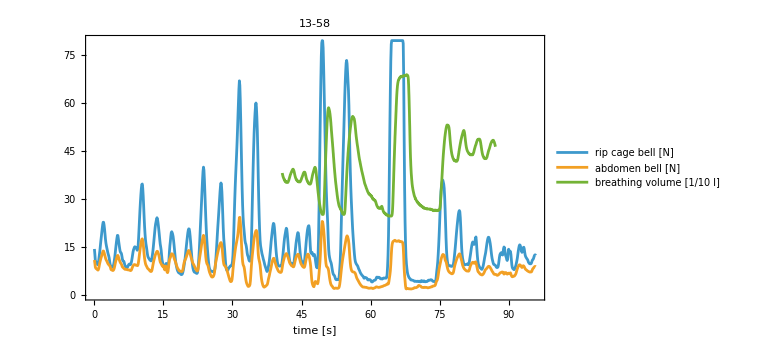
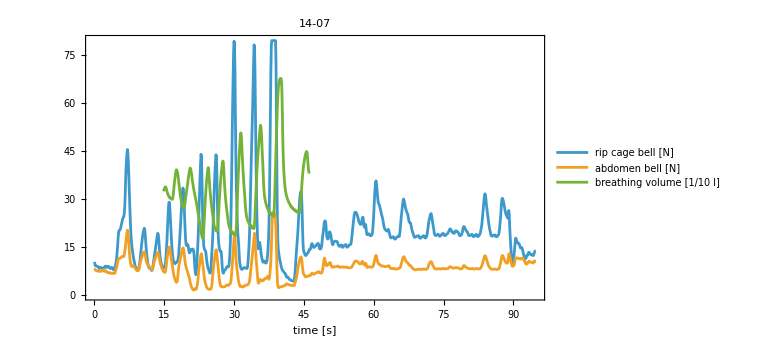
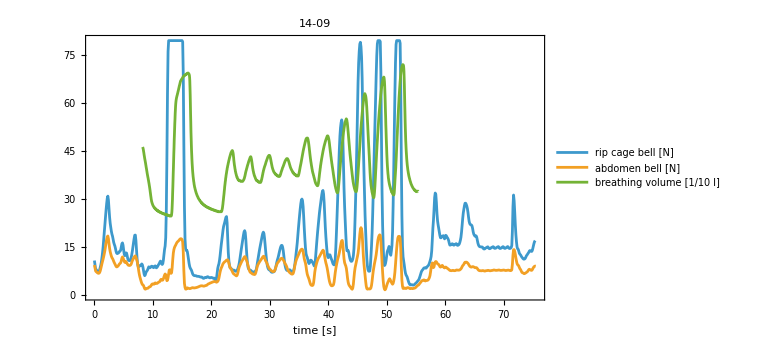
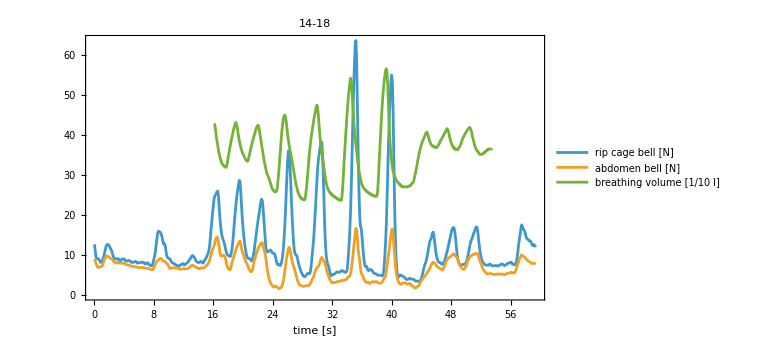
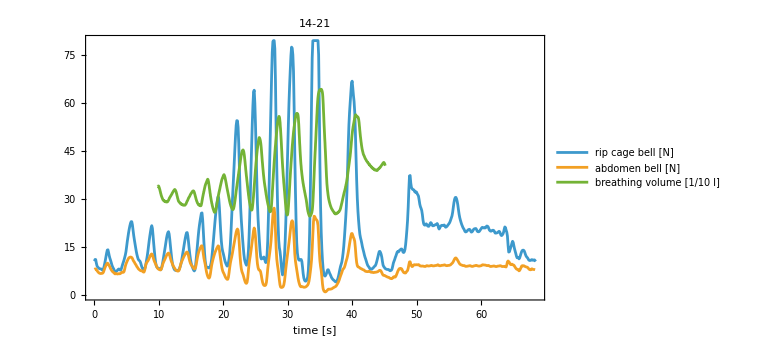

```mathematica
dataForAnalysis=Transpose[{evaluableData,evaluableData/.ripData,evaluableData /. spiroDataTimeCalibratedSmoothed}];
dataForAnalysis[[All,2]]=Map[Transpose[{{#[[1]],#[[2]]},{#[[1]],#[[3]]}}&/@(Flatten[#,1])] /. Missing["NotAvailable"]->Null&,dataForAnalysis[[All,{2}]]];

ListPlot[Append[#[[2]],{#[[1]],#[[2]]*10}&/@#[[3]]],PlotLabel->myStyle@#[[1]],PlotRange->All,PlotLegends->{"rip cage bell [N]","abdomen bell [N]","breathing volume [1/10 l]"},FrameLabel->{"time [s]",None},ImageSize->Large,Frame->True,Joined->True,myFrameStyle[],myFrameTickStyle[], myPlotStyle[]]&/@dataForAnalysis
```

```mathematica
dataForAnalysis={#[[1]],Append[#[[2]],#[[3]]]}&/@dataForAnalysis (*time stamp, {rip, abdomen, spiro}*)
```

{{{41.8813,3.51695},{43.1813,3.9322}},{{44.5147,3.5339},{45.648,3.83898}},{{46.8147,3.4661},{47.9147,3.99153}},{{49.6147,2.51695},{50.8813,5.85593}},{{54.2147,2.51695},{56.1147,5.58475}},{{64.2147,2.4661},{67.8147,6.88136}},{{74.4147,2.63559},{76.6813,5.31356}},{{78.648,4.17797},{80.248,5.14407}},{{81.9147,4.38136},{83.5813,4.87288}},{{84.9813,4.26271},{86.648,4.83898}}}

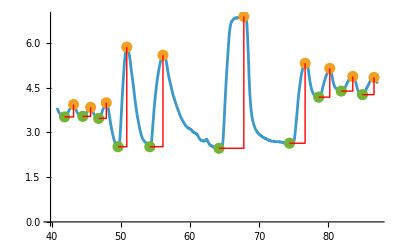

```mathematica
values=dataForAnalysis[[1,2,3]];
peaks=FindPeaks[dataForAnalysis[[1,2,3]][[All,2]],10];
peaksLow=FindPeaks[-dataForAnalysis[[1,2,3]][[All,2]],10];

If[peaks[[1,1]]<peaksLow[[1,1]],peaks=Delete[peaks,1],Nothing] ;(*start with first inspiration volume*)

peaksLow=peaksLow[[1;;Length[peaks]]];


peaksLow=peaksLow[[1;;Length[peaks]]];

xdiffs=Transpose[{values[[Round[#[[1]]]]]&/@peaksLow,values[[Round[#[[1]]]]]&/@peaks}]
xdiffsLine={#[[1]],{#[[2,1]],
#[[1,2]]},#[[2]]}&/@xdiffs;
linesDiff=Line/@xdiffsLine;
xDiffSeconds=-Subtract@@@xdiffs[[All,All,1]]; (*inspiratory breathing duration*)
yDiffVolume=-Subtract@@@xdiffs[[All,All,2]] ;(*inspiratory breathing volume*)

Tabular[Transpose[{xDiffSeconds,yDiffVolume}],{"Δ insp. time [s]","Δ insp. volume [l]"}]

Show[
ListLinePlot[
{values,values[[Round@#]]&/@ peaks[[All,1]],values[[Round@#]]&/@ peaksLow[[All,1]]},
Joined->{True,False,False},
PlotStyle->{Automatic,PointSize[.02],PointSize[.02],PlotRange->All}
]
,Graphics[{Thick,Red,#}]&/@linesDiff
]
```

breaths from spirometry

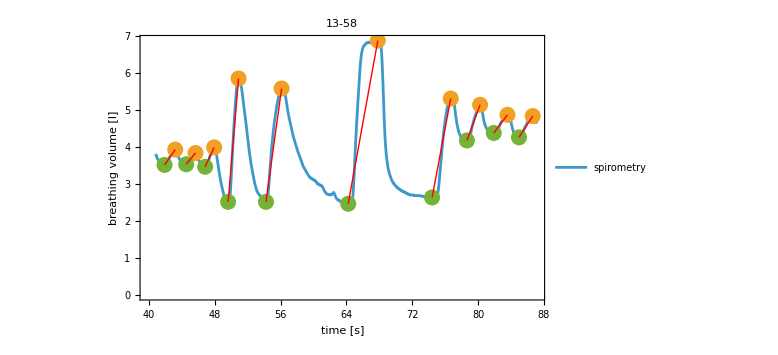
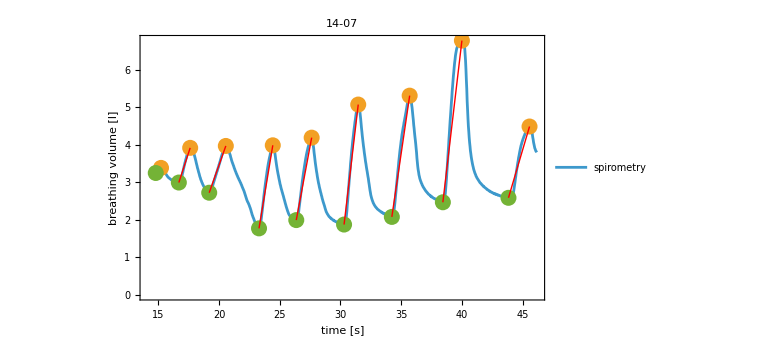
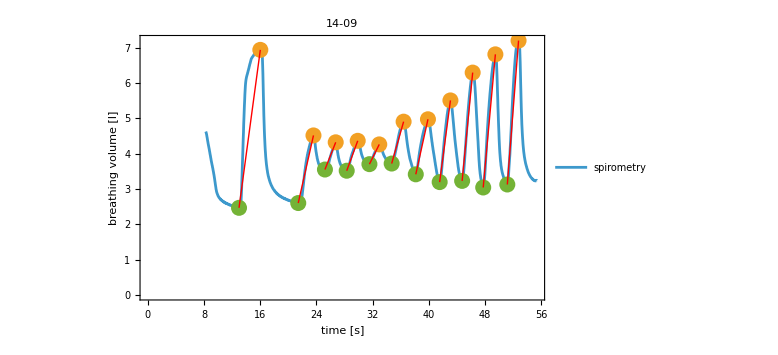
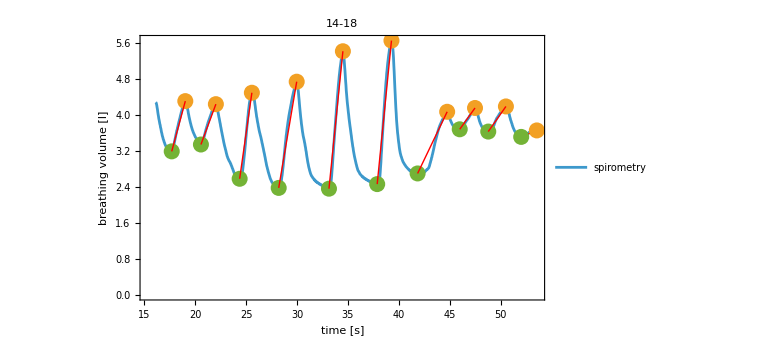
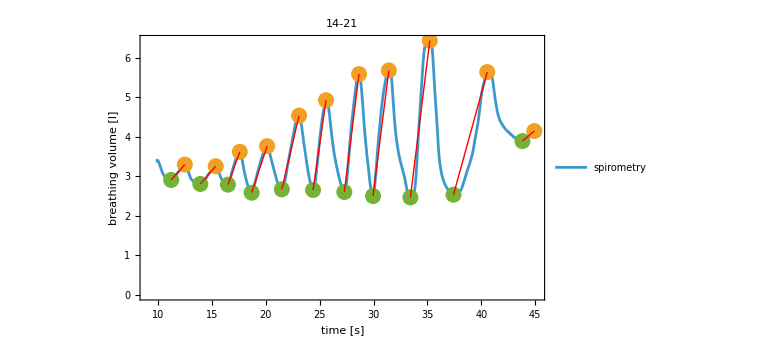

```mathematica
breathDetect=.
breathDetect[l_]:=Module[{peaks,peaksLow,xdiffs,linesDiff,xDiffSeconds,yDiffVolume}
,values=l[[2,3]];
peaks=FindPeaks[l[[2,3]][[All,2]],10];
peaksLow=FindPeaks[-l[[2,3]][[All,2]],10];

If[peaks[[1,1]]<peaksLow[[1,1]],peaks=Delete[peaks,1],Nothing] ;(*start with first inspiration volume*)

peaksLow=peaksLow[[1;;Length[peaks]]];


peaksLow=peaksLow[[1;;Length[peaks]]];

xdiffs=Transpose[{values[[Round[#[[1]]]]]&/@peaksLow,values[[Round[#[[1]]]]]&/@peaks}];
linesDiff=Line/@xdiffs;
xDiffSeconds=-Subtract@@@xdiffs[[All,All,1]]; (*inspiratory breathing duration*)
yDiffVolume=-Subtract@@@xdiffs[[All,All,2]] ;(*inspiratory breathing volume*)

{Tabular[Transpose[{xDiffSeconds,yDiffVolume}],{"Δ insp. time [s]","Δ insp. volume [l]"}],

Show[
ListLinePlot[
{values,values[[Round@#]]&/@ peaks[[All,1]],values[[Round@#]]&/@ peaksLow[[All,1]]},PlotLabel->myStyle@l[[1]],PlotLegends->{"spirometry"},FrameLabel->{"time [s]","breathing volume [l]"},
Joined->{True,False,False},
PlotStyle->{Automatic,PointSize[.02],PointSize[.02],PlotRange->All},ImageSize->Large,Frame->True,myFrameStyle[],myFrameTickStyle[]
]
,Graphics[{Thick,Red,#}]&/@linesDiff
]}
]

spiroBreaths=breathDetect/@ dataForAnalysis
```

breaths from RIP

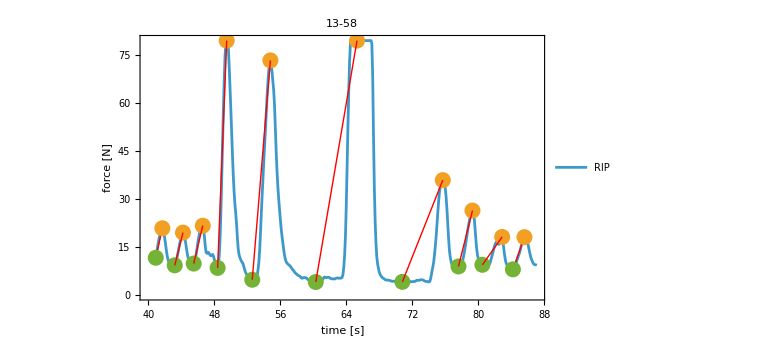
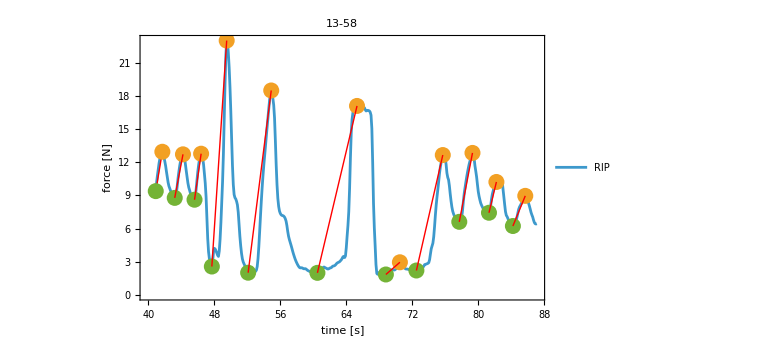
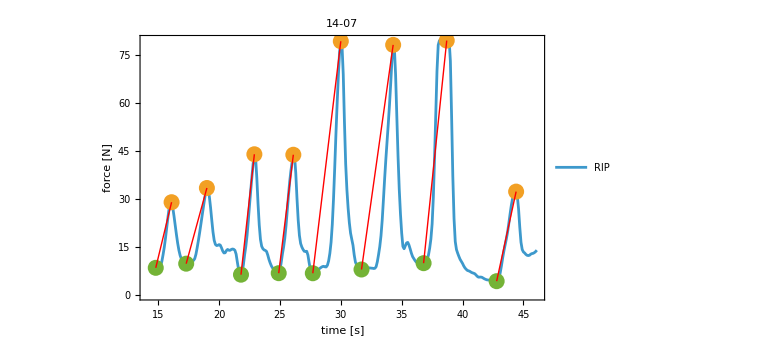
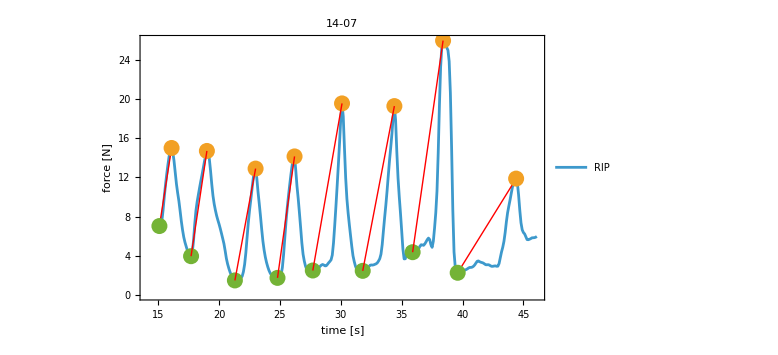
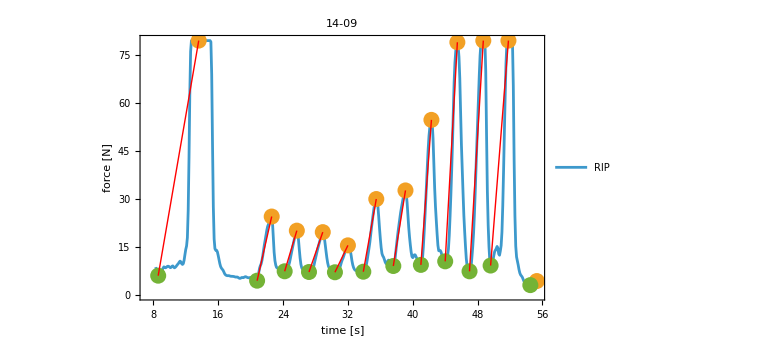
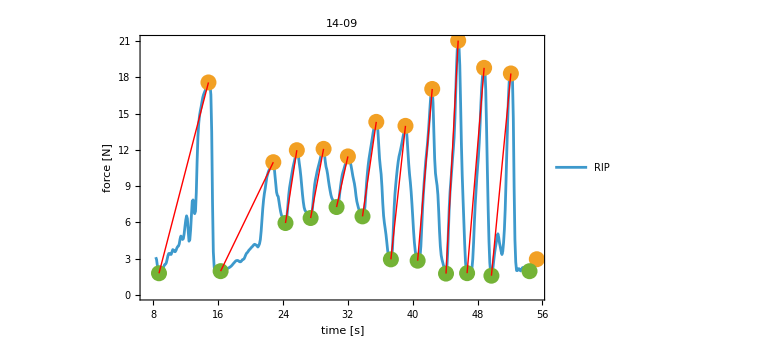
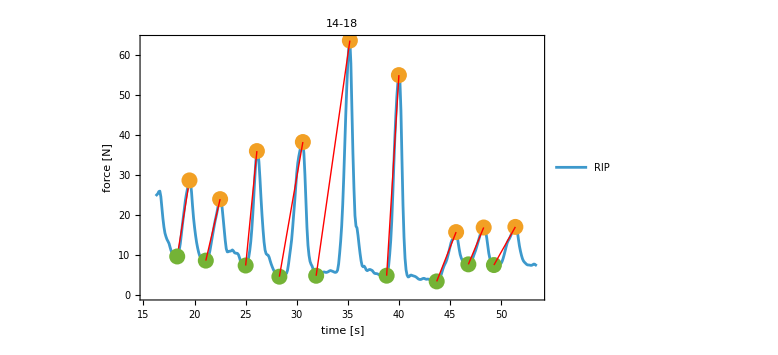
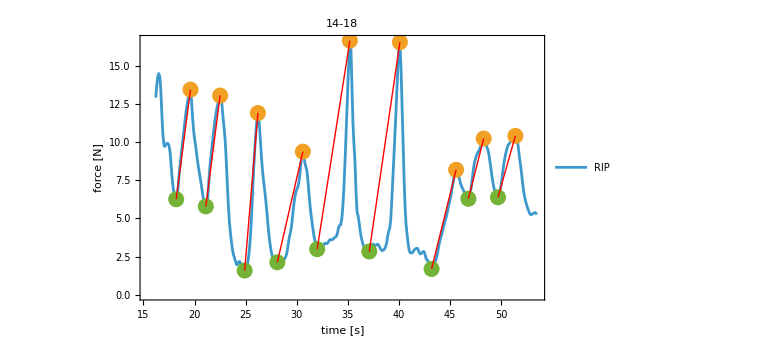

```mathematica
dataForAnalysisCropped=dataForAnalysis;
Table[
{lbound,ubound}=dataForAnalysisCropped[[i,2,3]][[{1,-1}]][[All,1]];
dataForAnalysisCropped[[i,2,1]]=Select[dataForAnalysisCropped[[i,2,1]],lbound<#[[1]]<ubound&];
dataForAnalysisCropped[[i,2,2]]=Select[dataForAnalysisCropped[[i,2,2]],lbound<#[[1]]<ubound&];
,{i,Length@dataForAnalysisCropped}];

breathDetect=.
breathDetect[l_]:=Module[{peaks,peaksLow,xdiffs,linesDiff,xDiffSeconds,yDiffVolume}
,
Table[values=l[[2,i]];
peaks=FindPeaks[l[[2,i]][[All,2]],6];
peaksLow=FindPeaks[-l[[2,i]][[All,2]],6];

If[peaks[[1,1]]<peaksLow[[1,1]],peaks=Delete[peaks,1],Nothing] ;(*start with first inspiration volume*)
(*hier noch prüfen, ob der Peak im Zeitverlauf auch nahe am Peak der Spirometrie liegt!!! 10%?*)
peaksLow=peaksLow[[1;;Length[peaks]]];


peaksLow=peaksLow[[1;;Length[peaks]]];

xdiffs=Transpose[{values[[Round[#[[1]]]]]&/@peaksLow,values[[Round[#[[1]]]]]&/@peaks}];
linesDiff=Line/@xdiffs;
xDiffSeconds=-Subtract@@@xdiffs[[All,All,1]]; (*inspiratory breathing duration*)
yDiffVolume=-Subtract@@@xdiffs[[All,All,2]] ;(*inspiratory breathing volume*)

{Tabular[Transpose[{xDiffSeconds,yDiffVolume}],{"Δ insp. time [s]","Δ force [N]"}]
,Show[
ListLinePlot[
{values,values[[Round@#]]&/@ peaks[[All,1]],values[[Round@#]]&/@ peaksLow[[All,1]]},PlotLabel->myStyle@l[[1]],
PlotLegends->{"RIP"},FrameLabel->{"time [s]","force [N]"},
Joined->{True,False,False},
PlotStyle->{Automatic,PointSize[.02],PointSize[.02],PlotRange->All},ImageSize->Large,Frame->True,PlotRange->All,myFrameStyle[],myFrameTickStyle[]
]
,Graphics[{Thick,Red,#}]&/@linesDiff
]
}
,{i,{1,2}}]

]

ripBreaths=breathDetect/@dataForAnalysisCropped
```

```mathematica
Transpose[{spiroBreaths[[All,2]],ripBreaths[[All,All,2]]}]
```

{{-Graphics-,{-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-}}}

```mathematica
dCorrelation=Flatten/@Transpose[{spiroBreaths[[All,1]],ripBreaths[[All,All,1]]}]
```

{{,,},{,,},{,,},{,,},{,,}}

```mathematica
myTabularNormal=.
myTabularNormal[t_]:=Module[{},If[TabularQ[t],Values/@(Normal@t),Values/@(Normal/@t)]]
```

```mathematica
spiroBreaths[[1,2]]
```

-Graphics-

```mathematica
myPlotLabelAndLegend[plotLabel_,plotLegend_List,frameLabel_List]:=Sequence[PlotLabel->myStyle@plotLabel,
PlotLegends->myStyle/@plotLegend,FrameLabel->frameLabel]
```

```mathematica
myPlotConfig=.
myPlotConfig=Sequence[PlotRange->All,Frame->True,ImageSize->Large,myFrameStyle[],myFrameTickStyle[]]
```

Sequence[PlotRange→All,Frame→True,ImageSize→Large,FrameStyle→Directive[FontSize→15,FontFamily→Lucida Sans Unicode,GrayLevel[0]],FrameTicksStyle→Directive[FontSize→15,FontFamily→Lucida Sans Unicode,GrayLevel[0]]]

```mathematica
myPlotLabelAndLegend["13-58",{"correlation spirometry and RIP"},{"force [N]","breathing volume [l]"}]
```

Sequence[PlotLabel→13-58,PlotLegends→{correlation spirometry and RIP},FrameLabel→{force [N],breathing volume [l]}]

{10,10,10}

{{{1.3,0.8,0.8},{0.415254,9.22866,3.55912}},{{1.13333,1.,1.},{0.305085,10.2353,3.93726}},{{1.1,1.1,0.8},{0.525424,11.845,4.15954}},{{1.26667,1.1,1.8},{3.33898,71.1057,20.4221}},{{1.9,2.2,2.8},{3.0678,68.6171,16.4721}},{{3.6,5.,4.8},{4.41525,75.5309,15.0873}},{{2.26667,4.9,3.2},{2.67797,31.8302,10.4372}},{{1.6,1.7,1.6},{0.966102,17.4915,6.22909}},{{1.66667,2.4,0.9},{0.491525,8.71255,2.78239}},{{1.66667,1.4,1.5},{0.576271,10.0641,2.72619}}}

FittedModel[…]

{0.0659819+0.0512292 x-2.306 √(0.0500649-0.00182165 x+0.0000289463 x^2),0.0659819+0.0512292 x+2.306 √(0.0500649-0.00182165 x+0.0000289463 x^2)}

{,}

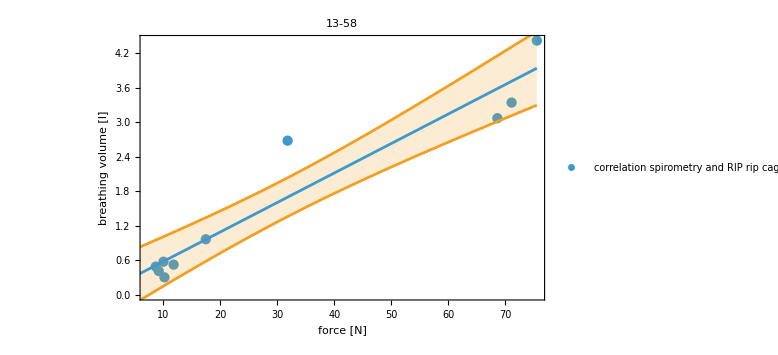

```mathematica
temp=myTabularNormal[dCorrelation[[1]]];
temp[[3]] = Select[temp[[3]],#[[2]]>1.5&];
Length/@temp
temp=Transpose/@Transpose[temp]
lnm=LinearModelFit[temp[[All,2]][[All,{2,1}]],x,x]
lnm["MeanPredictionBands",ConfidenceLevel->.95]
lnm[{"ParameterEstimates","MeanPredictions"}]
bands95[x_]=lnm["MeanPredictionBands",ConfidenceLevel->.95];

Show[ListPlot[temp[[All,2]][[All,{2,1}]],myPlotLabelAndLegend["13-58",{"correlation spirometry and RIP rip cage"},{"force [N]","breathing volume [l]"}],myPlotConfig],Plot[{lnm[x],bands95[x]},{x,Min@temp[[All,2]][[All,{2,1}]],Max@temp[[All,2]][[All,{2,1}]]},Filling->{2->{1}}]]
```

manuelle Anpassung, siehe auch Transpose[{spiroBreaths[[All,2]],ripBreaths[[All,All,2]]}]

13 - 58 delete 7 bei abdomen
14-07 delete 1 bei spiro
14 - 09 delete - 1 bei cage und abdomen
14 - 18 delete - 1 bei spirometry
14-21 delete -1 bei spirometry und cage

```mathematica
evaluableData
```

{13-58,14-07,14-09,14-18,14-21}

```mathematica
dCorrelationElected=myTabularNormal/@dCorrelation;
dCorrelationElected=Delete[dCorrelationElected,{{1,3,7},{2,1,1},{3,2,-1},{3,3,-1},{4,1,-1},{5,1,-1},{5,2,-1}}];
Map[Length,dCorrelationElected,{2}]
dCorrelationElected=myFlatten[Transpose[dCorrelationElected][[All,All,All,2]],1];
```

{{10,10,10},{8,8,8},{11,11,11},{9,9,9},{10,10,10}}

FittedModel[…]

FittedModel[…]

{0.90628,0.904242}

0.156586

{{0.181881+0.0487349 x-2.0129 √(0.0106415-0.000396996 x+5.33942×10^-6 x^2),0.181881+0.0487349 x+2.0129 √(0.0106415-0.000396996 x+5.33942×10^-6 x^2)},}

{,}

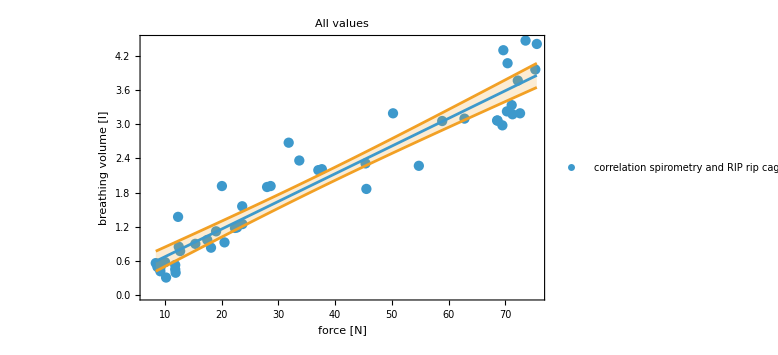

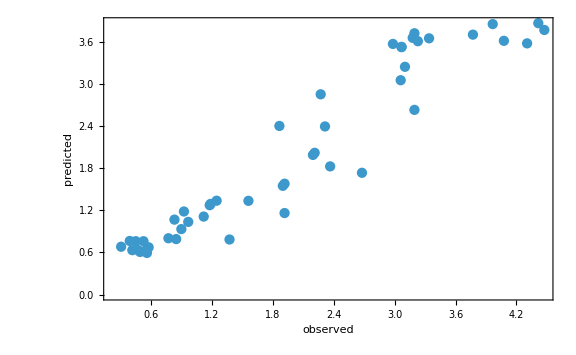

```mathematica
lnmRipCageGetForce=LinearModelFit[Transpose[dCorrelationElected[[{1,2}]]],x,x] (*volume in Newton out*)
fitData=Transpose[dCorrelationElected[[{2,1}]]];
lnmRipCageGetVolume=lnm=LinearModelFit[fitData,x,x]
lnm[{"RSquared","AdjustedRSquared"}]
lnm["EstimatedVariance"]
lnm[{"MeanPredictionBands","SinglePredictions"},ConfidenceLevel->.95] (*https://www.graphpad.com/support/faqid/1506/  Prediciton = wo die nächsten Datenpunkte mit 95% Wahrscheinlichkeit liegen werden, Confidence = wo die aktuellen Daten zu 95% liegen and https://en.wikipedia.org/wiki/Confidence_and_prediction_bands#Prediction_bands*)
lnm[{"ParameterEstimates","MeanPredictions"}]
bands95[x_]=lnm["MeanPredictionBands",ConfidenceLevel->.95];

Show[ListPlot[fitData,myPlotLabelAndLegend["All values",{"correlation spirometry and RIP rip cage"},{"force [N]","breathing volume [l]"}],myPlotConfig],Plot[{lnm[x],bands95[x]},{x,Min@fitData[[All,1]],Max@fitData[[All,1]]},Filling->{2->{1}}]]

ListPlot[Transpose[lnm[{"Response","PredictedResponse"}]],FrameLabel->{"observed","predicted"},myPlotConfig]
```

```mathematica
Min@fitData[[All,1]]
```

8.41872

FittedModel[…]

FittedModel[…]

{0.773369,0.768442}

0.37865

{{-0.123767+0.187762 x-2.0129 √(0.0364504-0.00506547 x+0.000224591 x^2),-0.123767+0.187762 x+2.0129 √(0.0364504-0.00506547 x+0.000224591 x^2)},}

{,}

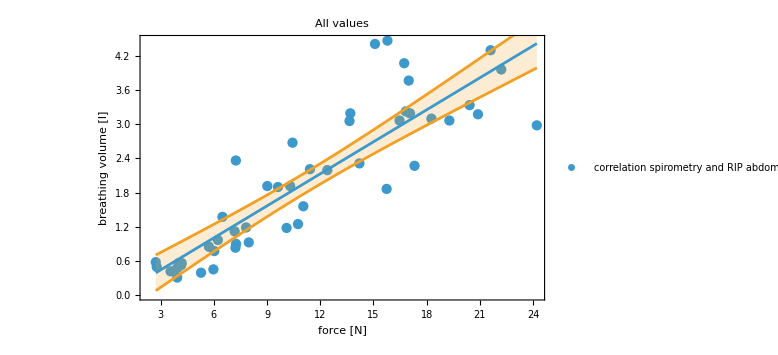

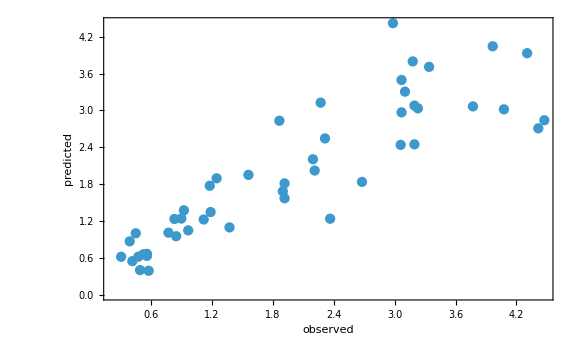

```mathematica
lnmAbdomenGetForce=LinearModelFit[Transpose[dCorrelationElected[[{1,3}]]],x,x]
fitData=Transpose[dCorrelationElected[[{3,1}]]];
lnmAbdomenGetVolume=lnm=LinearModelFit[fitData,x,x]
lnm[{"RSquared","AdjustedRSquared"}]
lnm["EstimatedVariance"]
lnm[{"MeanPredictionBands","SinglePredictions"},ConfidenceLevel->.95]
lnm[{"ParameterEstimates","MeanPredictions"}]
bands95[x_]=lnm["MeanPredictionBands",ConfidenceLevel->.95];

Show[ListPlot[fitData,myPlotLabelAndLegend["All values",{"correlation spirometry and RIP abdomen"},{"force [N]","breathing volume [l]"}],myPlotConfig],Plot[{lnm[x],bands95[x]},{x,Min@fitData[[All,1]],Max@fitData[[All,1]]},Filling->{2->{1}}]]

ListPlot[Transpose[lnm[{"Response","PredictedResponse"}]],FrameLabel->{"observed","predicted"},myPlotConfig]
```

```mathematica
newtonFromRIPripcage=.
newtonFromRIPripcage[v_]:=Module[{},Around[lnmRipCageGetForce[v],(Subtract@@Reverse@(lnmRipCageGetForce["MeanPredictionBands",ConfidenceLevel->.95] /. x->v))/2]]
{#,newtonFromRIPcage[#]}&/@{3,5}
```

{{3,newtonFromRIPcage[3]},{5,newtonFromRIPcage[5]}}

```mathematica
volumeFromRIPripcage=.
volumeFromRIPripcage[f_]:=Module[{},Around[lnmRipCageGetVolume[f],(Subtract@@Reverse@(lnmRipCageGetVolume["MeanPredictionBands",ConfidenceLevel->.95] /. x->f))/2]]
{#,newtonFromRIPcage[#]}&/@{20,40,60}
```

{{20,newtonFromRIPcage[20]},{40,newtonFromRIPcage[40]},{60,newtonFromRIPcage[60]}}

-Graphics--Graphics-
aus
 https://publikationen.dguv.de/widgets/pdf/download/article/1011%7CDGUV-Regel112-190_Benutzung-von-Atemschutzgeraeten_Download.pdf

Zielwerte: 30 und 50 l/min  Atemminutenvolumen

```mathematica
af=Range[10,70,5] (*Atemfrequenz*)
```

{10,15,20,25,30,35,40,45,50,55,60,65,70}

```mathematica
Print[myStyle["values for 30 l/min"]]
TableForm[{af,30./af,newtonFromRIPripcage/@(30./af)},TableHeadings->{{"respiratory rate [min^-1 ]","breathing volume [l]","force of RIP of ripcage [N]"},None}]
```

values for 30 l/min

respiratory rate [min^-1 ] | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60 | 65 | 70
breathing volume [l] | 3. | 2. | 1.5 | 1.2 | 1. | 0.857143 | 0.75 | 0.666667 | 0.6 | 0.545455 | 0.5 | 0.461538 | 0.428571
force of RIP of ripcage [N] | 55.92.9 | 37.32.2 | 28.02.4 | 22.42.7 | 18.72.9 | 16.03.0 | 14.03.1 | 12.53.3 | 11.33.3 | 10.23.4 | 9.43.5 | 8.73.5 | 8.4.

```mathematica
Print[myStyle["values for 50 l/min"]]
TableForm[{af,50./af,newtonFromRIPripcage/@(50./af)},TableHeadings->{{"respiratory rate [min^-1 ]","breathing volume [l]","force of RIP of ripcage [N]"},None}]
```

values for 50 l/min

respiratory rate [min^-1 ] | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60 | 65 | 70
breathing volume [l] | 5. | 3.33333 | 2.5 | 2. | 1.66667 | 1.42857 | 1.25 | 1.11111 | 1. | 0.909091 | 0.833333 | 0.769231 | 0.714286
force of RIP of ripcage [N] | 93.6. | 62.13.3 | 46.62.4 | 37.32.2 | 31.12.3 | 26.72.5 | 23.32.6 | 20.82.7 | 18.72.9 | 17.03.0 | 15.63.0 | 14.43.1 | 13.43.2

```mathematica
calculateMinuteVentilation=.
calculateMinuteVentilation[af_,f_]:=Module[{},volumeFromRIPripcage[f]*af]
Print[myStyle["values for 30 l/min"]]
corr=1
Labeled[TableForm[(Table[If[Between[30,{#[[1]]-#[[2]]corr,#[[1]]+#[[2]]corr}],Style[#,Background->Green],#]&@calculateMinuteVentilation[rf,f],{rf,af},{f,frange=Range[10,80,5]}]),TableHeadings->{af,frange}],{"force of RIP ripcage","respiratory rate"},{Top,Left}]
```

values for 30 l/min

1

| 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60 | 65 | 70 | 75 | 80
10 | 6.71.7 | 9.11.5 | 11.61.4 | 14.01.3 | 16.41.2 | 18.91.2 | 21.31.2 | 23.71.2 | 26.21.3 | 28.61.4 | 31.11.6 | 33.51.7 | 35.91.9 | 38.42.1 | 40.82.3
15 | 10.02.6 | 13.72.3 | 17.32.1 | 21.01.9 | 24.71.8 | 28.31.7 | 32.01.7 | 35.61.8 | 39.31.9 | 42.92.1 | 46.62.3 | 50.22.6 | 53.92.9 | 57.63.2 | 61.23.4
20 | 13.43.4 | 18.33.1 | 23.12.8 | 28.02.6 | 32.92.4 | 37.82.3 | 42.62.3 | 47.52.4 | 52.42.6 | 57.22.8 | 62.13.1 | 67.03.5 | 72.4. | 77.4. | 82.5.
25 | 17.4. | 23.4. | 28.93.5 | 35.03.2 | 41.13.0 | 47.22.9 | 53.32.9 | 59.43.0 | 65.53.2 | 71.63.5 | 78.4. | 84.4. | 90.5. | 96.5. | 102.6.
30 | 20.5. | 27.5. | 35.4. | 42.4. | 49.4. | 56.63.5 | 63.93.5 | 71.4. | 79.4. | 86.4. | 93.5. | 100.5. | 108.6. | 115.6. | 122.7.
35 | 23.6. | 32.5. | 40.5. | 49.4. | 58.4. | 66.4. | 75.4. | 83.4. | 92.5. | 100.5. | 109.5. | 117.6. | 126.7. | 134.7. | 143.8.
40 | 27.7. | 37.6. | 46.6. | 56.5. | 66.5. | 76.5. | 85.5. | 95.5. | 105.5. | 114.6. | 124.6. | 134.7. | 144.8. | 153.8. | 163.9.
45 | 30.8. | 41.7. | 52.6. | 63.6. | 74.5. | 85.5. | 96.5. | 107.5. | 118.6. | 129.6. | 140.7. | 151.8. | 162.9. | 173.9. | 184.10.
50 | 33.9. | 46.8. | 58.7. | 70.6. | 82.6. | 94.6. | 107.6. | 119.6. | 131.6. | 143.7. | 155.8. | 167.9. | 180.10. | 192.11. | 204.11.
55 | 37.9. | 50.8. | 64.8. | 77.7. | 90.7. | 104.6. | 117.6. | 131.7. | 144.7. | 157.8. | 171.9. | 184.10. | 198.11. | 211.12. | 224.13.
60 | 40.10. | 55.9. | 69.8. | 84.8. | 99.7. | 113.7. | 128.7. | 142.7. | 157.8. | 172.9. | 186.9. | 201.10. | 216.11. | 230.13. | 245.14.
65 | 43.11. | 59.10. | 75.9. | 91.8. | 107.8. | 123.8. | 139.8. | 154.8. | 170.8. | 186.9. | 202.10. | 218.11. | 234.12. | 249.14. | 265.15.
70 | 47.12. | 64.11. | 81.10. | 98.9. | 115.8. | 132.8. | 149.8. | 166.8. | 183.9. | 200.10. | 217.11. | 234.12. | 252.13. | 269.15. | 286.16.force of RIP ripcagerespiratory rate

```mathematica
calculateMinuteVentilation=.
calculateMinuteVentilation[af_,f_]:=Module[{},volumeFromRIPripcage[f]*af]
Print[myStyle["values for 50 l/min"]]
corr=1
Labeled[TableForm[(Table[If[Between[50,{#[[1]]-#[[2]] corr,#[[1]]+#[[2]] corr}],Style[#,Background->Green],#]&@calculateMinuteVentilation[rf,f],{rf,af},{f,frange=Range[10,80,5]}]),TableHeadings->{af,frange}],{"force of RIP ripcage","respiratory rate"},{Top,Left}]
```

values for 50 l/min

1

| 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60 | 65 | 70 | 75 | 80
10 | 6.71.7 | 9.11.5 | 11.61.4 | 14.01.3 | 16.41.2 | 18.91.2 | 21.31.2 | 23.71.2 | 26.21.3 | 28.61.4 | 31.11.6 | 33.51.7 | 35.91.9 | 38.42.1 | 40.82.3
15 | 10.02.6 | 13.72.3 | 17.32.1 | 21.01.9 | 24.71.8 | 28.31.7 | 32.01.7 | 35.61.8 | 39.31.9 | 42.92.1 | 46.62.3 | 50.22.6 | 53.92.9 | 57.63.2 | 61.23.4
20 | 13.43.4 | 18.33.1 | 23.12.8 | 28.02.6 | 32.92.4 | 37.82.3 | 42.62.3 | 47.52.4 | 52.42.6 | 57.22.8 | 62.13.1 | 67.03.5 | 72.4. | 77.4. | 82.5.
25 | 17.4. | 23.4. | 28.93.5 | 35.03.2 | 41.13.0 | 47.22.9 | 53.32.9 | 59.43.0 | 65.53.2 | 71.63.5 | 78.4. | 84.4. | 90.5. | 96.5. | 102.6.
30 | 20.5. | 27.5. | 35.4. | 42.4. | 49.4. | 56.63.5 | 63.93.5 | 71.4. | 79.4. | 86.4. | 93.5. | 100.5. | 108.6. | 115.6. | 122.7.
35 | 23.6. | 32.5. | 40.5. | 49.4. | 58.4. | 66.4. | 75.4. | 83.4. | 92.5. | 100.5. | 109.5. | 117.6. | 126.7. | 134.7. | 143.8.
40 | 27.7. | 37.6. | 46.6. | 56.5. | 66.5. | 76.5. | 85.5. | 95.5. | 105.5. | 114.6. | 124.6. | 134.7. | 144.8. | 153.8. | 163.9.
45 | 30.8. | 41.7. | 52.6. | 63.6. | 74.5. | 85.5. | 96.5. | 107.5. | 118.6. | 129.6. | 140.7. | 151.8. | 162.9. | 173.9. | 184.10.
50 | 33.9. | 46.8. | 58.7. | 70.6. | 82.6. | 94.6. | 107.6. | 119.6. | 131.6. | 143.7. | 155.8. | 167.9. | 180.10. | 192.11. | 204.11.
55 | 37.9. | 50.8. | 64.8. | 77.7. | 90.7. | 104.6. | 117.6. | 131.7. | 144.7. | 157.8. | 171.9. | 184.10. | 198.11. | 211.12. | 224.13.
60 | 40.10. | 55.9. | 69.8. | 84.8. | 99.7. | 113.7. | 128.7. | 142.7. | 157.8. | 172.9. | 186.9. | 201.10. | 216.11. | 230.13. | 245.14.
65 | 43.11. | 59.10. | 75.9. | 91.8. | 107.8. | 123.8. | 139.8. | 154.8. | 170.8. | 186.9. | 202.10. | 218.11. | 234.12. | 249.14. | 265.15.
70 | 47.12. | 64.11. | 81.10. | 98.9. | 115.8. | 132.8. | 149.8. | 166.8. | 183.9. | 200.10. | 217.11. | 234.12. | 252.13. | 269.15. | 286.16.force of RIP ripcagerespiratory rate